```mathematica
V0 = {0, 0};
V1 = {1, 0};
V2 = {1, 1};
gradF = {2 * Pi, 0};

Fs0[b0_, b1_, b2_] := 2 * Pi;
Fs1[b0_, b1_, b2_] := b2/(b0 + b2) * 2 * Pi;
Fs2[b0_, b1_, b2_] := b0/(b0  + b1) * 2 * Pi;
F0 = 0;
F1 = 2 * Pi;
F2 = 2 * Pi;
```

```mathematica
h[t_]:= t*t*(3-2*t);

(*Bi's formula*)
B0[b0_, b1_, b2_] := h[1 - b0] Fs0[b0, b1, b2] - b0  (1 - b0) (b1 *Dot[(V2 - V0), gradF] + b2 * Dot[(V1 - V0), gradF]);
B1[b0_, b1_, b2_] := h[1 - b1] Fs1[b0, b1, b2] - b1  (1 - b1) (b2 *Dot[(V0 - V1), gradF] + b0 * Dot[(V2 - V1), gradF]);
B2[b0_, b1_, b2_] := h[1 - b2] Fs2[b0, b1, b2] - b2  (1 - b2) (b0 *Dot[(V1 - V2), gradF] + b1 * Dot[(V0 - V2), gradF]);
```

```mathematica
(*Pi's formula*)
P0[b0_, b1_, b2_] := h[b0]* F0 + b0 * b0 (b1 *Dot[(V2 - V0), gradF] + b2 * Dot[(V1 - V0), gradF]);
P1[b0_, b1_, b2_] := h[b1]* F1 + b1 * b1(b2 *Dot[(V0 - V1), gradF] + b0 * Dot[(V2 - V1), gradF]);
P2[b0_, b1_, b2_] := h[b2]* F2 + b2 * b2 (b0 *Dot[(V1 - V2), gradF] + b1 * Dot[(V0 - V2), gradF]);
```

```mathematica
(*Di's formula*)
DF0[b0_, b1_, b2_] := B0[b0, b1, b2] + P0[b0, b1, b2];
DF1[b0_, b1_, b2_] := B1[b0, b1, b2] + P1[b0, b1, b2];
DF2[b0_, b1_, b2_] := B2[b0, b1, b2] + P2[b0, b1, b2];
```

```mathematica
(*final formula*)
DF[b0_, b1_, b2_] :=If[b0== 0, DF0[b0, b1, b2],                           (*b0==0*)
					If[b1 == 0,  DF1[b0, b1, b2],                    (*b0≠0, but b1==0*)
					If[b2 == 0, DF2[b0, b1, b2],                   (*b0≠0, b1≠0, but b2==0*)
					(b1^2 b2^2 DF0[b0, b1, b2] + b2^2 b0^2 DF1[b0, b1, b2] + b0^2 b1^2 DF2[b0, b1, b2])/(b1^2 b2^2 + b2^2 b0^2 + b0^2 b1^2)   (*b0b1b2≠0*)
]]];
```

```mathematica
DF[0, 1, 0]
```

2 π

```mathematica
DF1[0, 0, 1]
```

2 π

```mathematica
DF2[0, 0, 1]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

```mathematica
b1^2 b2^2 + b2^2 b0^2 + b0^2 b1^2 /. {b0-> 0, b1-> 0, b2-> 1}
```

0

```mathematica
DF[b0, b1, b2] // FullSimplify
```

(2 (2 b0^5 b1^2 b2^2+b1^3 b2^3-b0 b1^2 b2^2 (b1+b2) (-1+b1 b2)+b0^4 b1 (b1+b1^2 b2+b2^3+2 b1 b2^3)+b0^2 b1 b2^2 (b1+b2-2 b1^2 b2 (1+b2))+b0^3 b2 (b1^4 (1-2 b2)+3 b1^3 b2+b2^2+b1 b2^3+b1^2 (1-3 b2^2))) π)/((b0+b1) (b0+b2) (b1^2 b2^2+b0^2 (b1^2+b2^2)))

```mathematica
DF[7/10, 3/10, 0]
```

(7 π)/5

```mathematica
DF[b0, b1, 1 - b0 - b1] // FullSimplify
```

(2 (-(-1+b0)^3 b0^2-(-1+b0)^2 b0^2 (1+2 b0) b1+(1+(-1+b0) b0 (3+b0 (3+b0 (-11+4 b0)))) b1^2+2 (-1+(-1+b0) b0 (-2+5 (-1+b0) b0)) b1^3+(1+(-1+b0) b0 (1+8 b0)) b1^4+2 b0^2 b1^5) π)/(b0^4+2 b0^3 (-1+b1)+2 b0 (-1+b1) b1^2+(-1+b1)^2 b1^2+b0^2 (1+b1 (-2+3 b1)))

```mathematica
DF[3/10, 3/10, 4/10] //N
```

4.42765

```mathematica
projDF0[x_] := DF[0, x, 1-x];
projDF1[x_] := DF[x, 0, 1-x];
projDF2[x_] := DF[x, 1-x, 0];
```

```mathematica
Plot[projDF0[x], {x, 0, 1}]
```

-Graphics-

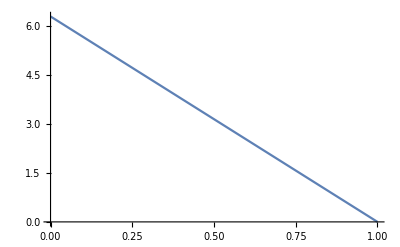

```mathematica
Plot[projDF1[x], {x, 0, 1}]
```

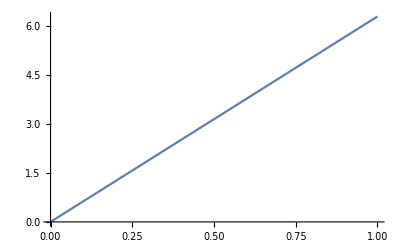

```mathematica
Plot[projDF2[x], {x, 0, 1}]
```

```mathematica
phiColor[ϕ_]:= Module[
{h, s, v}, 
h=360.0*ϕ/2.0/Pi+120;
h=360+(Mod[360, N[h]]);
Return [{h, 1.0, 0.5}]];
```

```mathematica
phiColor[2 * Pi]
```

{720.,1.,0.5}

```mathematica
xyY2XYZ[x_,y_,Y_]={(x Y)/y,Y,-(((-1+x+y) Y)/y)}
```

{(x Y)/y,Y,-((-1+x+y) Y)/y}

```mathematica
normalize[x_]:=x/Max@x
XYZ2sRGB[c_]:=(normalize[({{3.2406255,-1.537208,-0.4986286},{-0.9689307,1.8757561,0.0415175},{0.0557101,-0.2040211,1.0569959}}).c])^(1/2.2)
```

```mathematica
RegionPlot[DiscretizeRegion[Polygon[{V0, V1, V2}],MaxCellMeasure->{"Length"->0.05}],ColorFunction->Function[{x,y},Hue[phiColor[DF[1-x, x-y, y]]]],ColorFunctionScaling->False,BoundaryStyle->None]
```

-Graphics-

```mathematica
P0
```

P0